```mathematica
(*Free Electron on A Circular String Length L*)
```

```mathematica
A=1; B=2
```

2

```mathematica
L=4*Pi
```

4 π

```mathematica
n=2
```

2

```mathematica
ExpToTrig[A*Exp[I*2*Pi*nn*x/Ll]+ B*Exp[-I*2*Pi*nn*x/Ll]]
```

3 Cos[(2 nn π x)/Ll]-ⅈ Sin[(2 nn π x)/Ll]

```mathematica
Func:= A*Exp[I*2*Pi*n*x/L]+ B*Exp[-I*2*Pi*n*x/L]
```

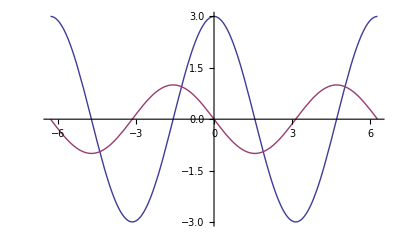

```mathematica
Plot[{Re[A*Exp[I*2*Pi*n*x/L]+ B*Exp[-I*2*Pi*n*x/L]],Im[A*Exp[I*2*Pi*n*x/L]+ B*Exp[-I*2*Pi*n*x/L]]},{x,-2*Pi,2*Pi}]
```

```mathematica
(* Func *Conjugate(Func)    Note ONLY REAL and also ONLY POSITIVE*)
```

```mathematica
DensityPsi=A*A +B*B+2*A*B*Cos[2*Pi*n*x/L]
```

5+4 Cos[x]

```mathematica
Plot[{Re[DensityPsi],Im[FuncTrig]},{x,-2*Pi,2*Pi}]
```

-Graphics-

```mathematica
A=1; B=1
```

1

```mathematica
(*  Set A =B  SINCE POSSIBLE AND EQUALLY LIKELY *)
```

```mathematica
Func:= A*Exp[I*2*Pi*n*x/L]+ A*Exp[-I*2*Pi*n*x/L]
```

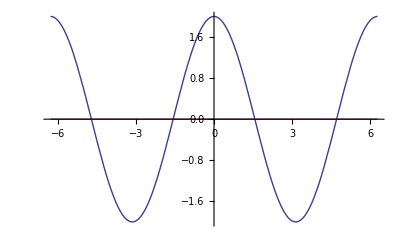

```mathematica
Plot[{Re[Func],Im[Func]},{x,-2*Pi,2*Pi}]
```

```mathematica
(*
NORMALIZE BY INTEGRATING OR ALL SPACE  *)
```

```mathematica
Integrate[ Func*Conjugate[Func],{x,-2*Pi,+2*Pi}]
```

8 π

```mathematica
(*    Thus   A^2 Psi^8*π   So  A = 1/Sqrt[8π] *)
```

```mathematica
Energy= 2*Pi^2*n^2*hbar^2/(m*L^2)
```

hbar^2/(2 m)

```mathematica
hbar= 1.05457173*10^-34
```

1.05457×10^-34

```mathematica
me= 9.10938291*10^-31
```

9.10938×10^-31

```mathematica
L= 10.0*10^-9
```

1.×10^-8

```mathematica
n=1
```

1

```mathematica
Energy1= 6.24150934*10^18* 2*Pi^2*n^2*hbar^2/(me*L^2)
```

0.0150412

```mathematica
n=2
```

2

```mathematica
Energy2= 6.24150934*10^18* 2*Pi^2*n^2*hbar^2/(me*L^2)
```

0.0601648

```mathematica
n=3
```

3

```mathematica
Energy3= 6.24150934*10^18* 2*Pi^2*n^2*hbar^2/(me*L^2)
```

0.135371

```mathematica
Delta12= Energy2-Energy1
```

0.0451236

```mathematica
Energy13=Energy3-Energy1
```

0.12033

```mathematica
HydrogenE= 13.6*(1/(1*1) - 1/(2*2))
```

10.2

```mathematica
(*   Work in ATOMIC UNITS  ---- Distance in a0 = 0.529 Ao  then hbar^2/me =1.00  Energy Unites called Hartrees    1Hartree =27.21 eV  *)v
```

v

```mathematica
LL=L/(0.52917721092*10^-10)
```

188.973

```mathematica
hbar =1
```

1

```mathematica
me=1
```

1

```mathematica
Energy= 2*Pi^2*n^2*hbar^2/(me*LL^2)
```

0.00497479

```mathematica
Energy*27.21
```

0.135364

```mathematica
Animate [Plot[(1/Sqrt[8*Pi])*(Exp[I*2*Pi*n*x/L]+ Exp[-I*2*Pi*n*x/L]),{x,-2*Pi,2*Pi}], {n,1,4},AnimationRunning ->False]

(*    Note that Wavefunction is only continuous around the circle (matches up)  if n is an integer at 1,2,3,4   *)
```

```mathematica
(*Particle in Box with Infinite Potential*)
```

```mathematica
L= 2*Pi
```

2 π

```mathematica
A=1
```

1

```mathematica
n=1
```

1

```mathematica
PSI= A*Sin[ n*Pi*x/L]
```

Sin[x/2]

```mathematica
Energy = Pi^2*hbar^2*n^2/(2*m*L^2)
```

1/(8 m)

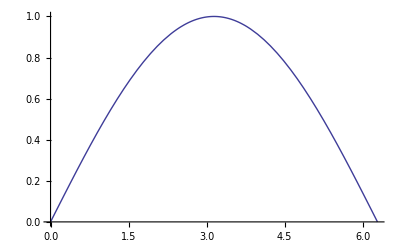

```mathematica
Plot[PSI,{x,0,L}]
```

```mathematica
Integrate [ Sin[n*Pi*x/LL]^2, { x,0,LL}]
```

94.4863

```mathematica
(*  Thus A = SQRT(2/L)  *)
```

```mathematica
Energy = Pi^2*hbar^2*n^2/(2*m*L^2)
```

1/(8 m)

```mathematica
NN[n]=Table[IntegerDigits[n],{n,9}]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9}}

```mathematica
EnergyS[n]=(Table[IntegerDigits[n],{n,9}])^2*Pi^2*hbar^2/(2ml^2)
```

{{π^2/(2 ml^2)},{(2 π^2)/ml^2},{(9 π^2)/(2 ml^2)},{(8 π^2)/ml^2},{(25 π^2)/(2 ml^2)},{(18 π^2)/ml^2},{(49 π^2)/(2 ml^2)},{(32 π^2)/ml^2},{(81 π^2)/(2 ml^2)}}

```mathematica
A=Sqrt[L/2]
```

√π

```mathematica
Animate[Plot[ A*Sin[ n*Pi*x/L],{x,0,L}],{n,1,9},AnimationRunning ->False]
```

```mathematica
n=2
```

2

```mathematica
Energy = Pi^2*hbar^2*n^2/(2*me*L^2)
```

1/2

```mathematica
N[1/2]
```

0.5

```mathematica
(*   BLUE IS REAl PSI and IMAGINARY PART IS RED *)
```

```mathematica
Animate[Plot[{ Sin[(n π x)/L] Cos[π^2 hbar n^2 t],A Sin[(n π x)/L] Sin[π^2 hbar n^2 t]},{x,0,L},PlotRange->{-2,2}],{n,1,9},{t,0,Pi/4},AnimationRunning->True]
```

```mathematica
t=Pi/3
```

π/3

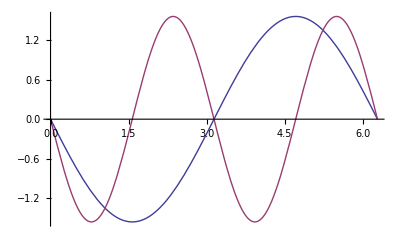

```mathematica
Plot[ {A*Sin[ n*Pi*x/L]*Cos[Pi^2*hbar*n^2*t],A*Sin[ 2n*Pi*x/L]*Cos[Pi^2*hbar*n^2*t]},{x,0,L}]
```

```mathematica
DESIREDPSI=  Exp[ -q*(x-L/2)^2]
```

ⅇ^(-q (-π+x)^2)

```mathematica
q=4
```

4

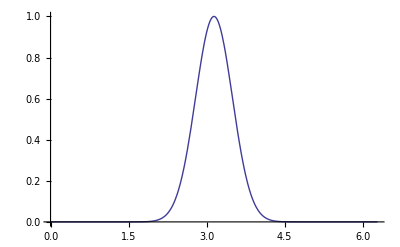

```mathematica
Plot[ⅇ^(-q (-π+x)^2),{x,0,L},PlotRange->{0,1}]
```

```mathematica
q=4
```

4

```mathematica
n=1
```

1

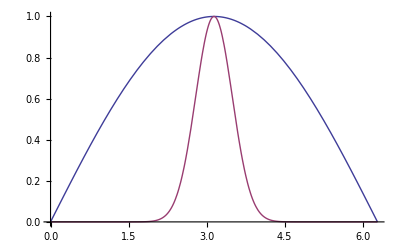

```mathematica
Plot[{Sin[(n π x)/L],ⅇ^(-q (x-(L/2))^2)},{x,0,L}]
```

```mathematica
n=3
```

3

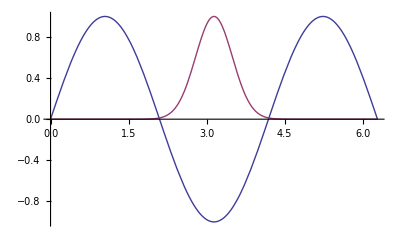

```mathematica
Plot[{Sin[(n π x)/L],ⅇ^(-q (x-(L/2))^2)},{x,0,L}]
```

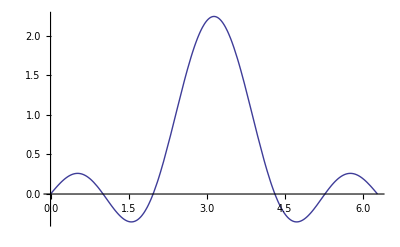

```mathematica
Plot[0.8724872504864979*Sin[(1 π x)/L]  -0.7699672960988844*Sin[(3 π x)/L]+ 0.5996511331411835*Sin[(5 π x)/L],{x,0,L}]
```

```mathematica
n=5
```

5

```mathematica
Re[N[Integrate[Sin[(n π x)/L]*ⅇ^(-q (x-(L/2))^2),{x,0,L}]]]
```

0.599651

```mathematica
Plot[0.8724872504864979*Sin[(1 π x)/L]  -0.7699672960988844*Sin[(3 π x)/L]+ 0.5996511331411835*Sin[(5 π x)/L],{x,0,L}]
```

-Graphics-